# Lista 1 - Introdução à Física Computacional I

## Marcos Vinícius Rodrigues Ribeiro

Problema 1.1

Para encontrar as seis correntes presentes no circuito, utilizou-se as Leis de Kirchoff,  dos nós e das malhas, desenvolvendo-se um sistema com seis equações, logo, solúvel.

```mathematica
eq1=i4==i2+i3;  
eq2=i1==i2+i5; 
eq3=i6==i1+i3;
eq4=0==V1-R1*i1+R3*i3-R2*i2;
eq5=0==R5*i5-R4*i4-R2*i2; 
eq6=0== V2-R4*i4-R3*i3-R6*i6;
```

Utilizando a função “Solve” é possível determinar as correntes em função das resistências e das forças eletromotrizes, onde todas as expressões são armazenadas em uma lista denonimada “correntes”. Basta indicar dentro da chamada da função quais variáveis deve expressar, nesse caso será i1, i2, i3, i4, i5 e i6, sendo o número da corrente respectivo ao resistor onde a corrente passa. A função “FullSimplify” possui o propósito de simplificar as expressões obtidas.

```mathematica
correntes=FullSimplify[Solve[{eq1,eq2,eq3,eq4,eq5,eq6},{i1,i2,i3,i4,i5,i6}]]
```

{{i1→(R4 R5 V1+(R4+R5) R6 V1+R2 (R3+R4+R6) V1+R2 (R3+R4) V2+R3 (R4+R5) (V1+V2))/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6))),i2→(R5 R6 V1+R4 (R5+R6) V1-R1 R4 V2+R3 R5 (V1+V2))/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6))),i3→(-((R4 R5+(R2+R4+R5) R6) V1)+(R2 R5+R1 (R2+R4+R5)) V2)/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6))),i4→(-R2 R6 V1+R1 R5 V2+R2 (R1+R5) V2+R3 R5 (V1+V2))/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6))),i5→(R3 R4 V1+R2 (R3+R4+R6) V1+R2 R3 V2+(R1+R2+R3) R4 V2)/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6))),i6→(R2 (R3+R4) V1+R2 (R1+R3+R4+R5) V2+(R4+R5) (R1 V2+R3 (V1+V2)))/(R3 R4 R5+R2 (R3+R4) R5+R3 (R4+R5) R6+R2 (R3+R4+R5) R6+R1 (R4 R5+R3 (R4+R5)+(R4+R5) R6+R2 (R3+R4+R6)))}}

Problema 1.2

Para obter o valor da resistência R6 nas condições enunciadas, obtém-se os valores de corrente em função de R6 utilizando o operador “/.”, que efetua uma atribuição numérica aos valores de resistência e forças eletromotrizes, e armenou-se essas expressões em uma lista (NCorrentes).

```mathematica
NCorrentes=correntes/.{V1->12,V2->8,R1->20,R2->15,R3->3,R4->6,R5->12};
```

Com a lista de correntes em função de R6, a expressão para a corrente que passa no resistor 3 é atribuída a uma variável usando a notação (NCorrentes[[1,3]]) e o operador “/.”, e com isso a função “Solve” é chamada para encontrar um valor de R6(indicado na chamada da função) com a condição de: i3 = 0.

```mathematica
i3deR6=i3/.NCorrentes[[1,3]];
R6dei3=Solve[i3deR6==0,R6];
```

Por fim, o valor numérico de resistência em Ohms pode ser obtido com a função “N” e novamente e extraindo o valor da lista de solução com uma atribuição temporária.

```mathematica
N[i3deR60=R6/.R6dei3]
```

{14.7879}

Problema 1.3

O processo é análogo ao item anterior

```mathematica
i4deR6=i4/.Correntes[[1,4]];
R6dei4=Solve[i4deR6==0,R6];
N[i4deR60=R6/.R6dei4]
```

{36.}

Problema 1.4

Usando a atribuição temporária é obtida a expressão das correntes que passam nos resistores 3, 4 e 5, correntes estas que estão armazenada na lista “NCorrentes”. Com isso, os gráficos são gerados com a função “Plot”, que em sua chamada pode ser incluída um série de alterações estéticas, como o “PlotLegends”,  que produz uma legenda e o “AxesLabel” que nomeia os eixos e “HoldForm” que imprime o input de forma “estilizada”, o uso de aspas também foi implementado para que elementos do output continuassem idêntico ao input.

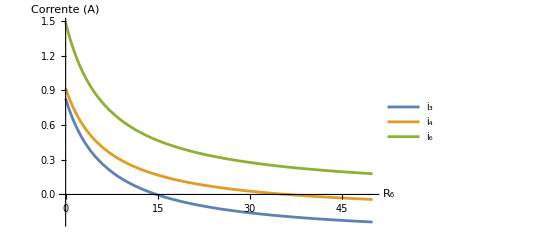

```mathematica
corrente3=i3/.NCorrentes[[1,3]];
corrente4=i4/.NCorrentes[[1,4]];
corrente6=i6/.NCorrentes[[1,6]];
Plot[{corrente3,corrente4,corrente6},{R6,0,50},PlotLegends->{HoldForm[Subscript["i",3]],HoldForm[Subscript["i",4]],HoldForm[Subscript["i",6]]}, AxesLabel->{HoldForm[Subscript[R,6]],"Corrente (A)"}]
(*As correntes possuem direção oposta, por isso inverti o sinal da corrente, que por uma suposição feita na hora de montar o sistema do Problema 1.1, o sinal sai invertido.*)
```

Problema 2.1

De início, os valores “l”, “g” e “x0” são classificados como constantes através da função “SetAttributes”. Também é criada uma expressão para pequenas oscilações, para uso posterior. Por fim, para obter uma expressão analítica do período é necessário chamar a função “Integrate”, onde pode ser incluída o limite de integração e a condição do enunciado  para a constante θ0.

```mathematica
SetAttributes[{l,g,θ0},Constant]; 
PeqOsci=2*Pi*Sqrt[l/g];
T=Sqrt[8*l/g]*Integrate[(1/(Sqrt[Cos[θ]-Cos[θ0]])),{θ,0,θ0}, Assumptions->0<θ0<π]
```

(4 √2 √(l/g) EllipticF[θ0/2,Csc[θ0/2]^2])/(√(1-Cos[θ0]))

Problema 2.2

Com os dados do enunciado é obtido o valor do período de oscilação utilizando a solução analítica obtida no item anterior. O cálculo é feito utilizando a atribuição temporária, citada anteriormente.

```mathematica
periodo1=T/.{l->1,g->9.8,θ0->(Pi/4)}
```

2.08732

Analogamente, fazendo as atribuições temporárias na expressão para pequenas oscilações.

```mathematica
periodo2=PeqOsci/.{l->1,g->9.8}
```

2.00709

Por fim, a razão entre o período calculado com a expressão baseada em conservação de energia mecânica e a expressão para pequenas oscilações pode ser calculada.

```mathematica
razao=periodo1/periodo2
```

1.03997

Problema 2.3

Para obter a solução numérica da equação diferencial, a função “NDSolve” é chamada. Nela, além de incluir a EDO, é necessário incluir as condições inicias do problema. E por meio da atribuição temporária também incluiu-se os valores numéricos das constantes. Também é necessário incluir o intervalo do qual se quer obter a função numérica que aproximará EDO.

```mathematica
Clear[θ]
sol=NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ'[0]==0,θ[0]==θ0}/.{l->1,g->9.8,θ0-> π/3},θ,{t,0,10*periodo1}]
```

{{θ→InterpolatingFunction[…]}}

Para extrair a solução da lista gerada pelo “NDSolve”, é necessário usar a atribuição temporária.

```mathematica
angulo[t_]:=θ[t]/.sol[[1]]
```

Novamente a função “Plot” pode ser usada para gerar o gráfico, onde elementos incluídos em sua chama alteram o gráfico. Como o “AxesLabel” que nomeia os eixos e o uso de aspas também foi implementado para que elementos do output continuassem idêntico ao input.

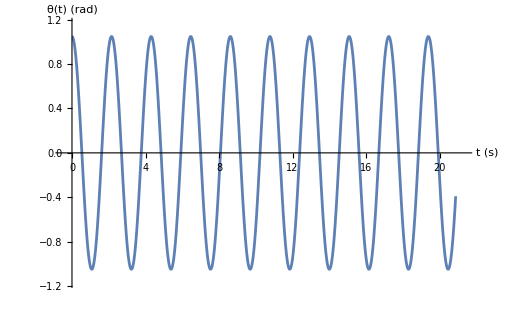

```mathematica
Plot[{angulo[t]},{t,0,10*periodo1},AxesLabel->{"t (s)","θ(t) (rad)"}]
```

Problema 3.1

Para encontrar uma solução analítica para a EDO enunciada, utiliza-se a função “DSolve”, onde é inserido a EDO em questão e sua condições iniciais, por fim indicando a variável . A função “FullSimplify” tem o objetivo de simplificar a equação obtida.

```mathematica
solLçVrt=FullSimplify[DSolve[{z''[t]==-g-γ*z'[t],z[0]==0,z'[0]==v0},z[t],t]]
```

{{z[t]→(g-g t γ+v0 γ-ⅇ^(-t γ) (g+v0 γ))/γ^2}}

A solução da EDO é gerada dentro de uma lista, para extraí-la defino uma nova variável que receberá o elemento no interior da lista, assim obtendo uma forma utilizável da solução, truque utilizado no problema 1 para extrair as expressões das correntes.

```mathematica
funcaoz=z[t]/.solLçVrt[[1]] ;
```

Utiliza-se a função “Limit” para aplicar o limite onde γ se anula. Verificando que a expressão se reduz ao resultado esperado.

```mathematica
limiteGamma= Limit[funcaoz, γ->0]
```

-(g t^2)/2+t v0

Problema 3.2

Definindo as constantes com “SetAttributes”, obtém-se a derivada da posição utilizando a função “D”, que só necessita da função que será derivada e em qual variável.

```mathematica
SetAttributes[{γ,v0},Constant]; 
vel=FullSimplify[D[funcaoz,t]];
```

O tempo de subida pode ser obtido igualando a derivada a zero, momento em que a velocidade é zero. Com isso, chama-se a função “Solve” impondo que o resultado será um valor real. Utiliza-se também a função “Normal” para remover o condicional que é incluso no output ao não utiliza-la. Como citado outras vezes, a expressão gerada  pelo uso da função “Solve” é armazenada em uma lista, para extraí-la de lá é necessário fazer uma atribuição, onde também foi incluído o “FullSimplify” para simplificar a expressão.

```mathematica
ts = Normal[Solve[vel==0,t,Reals]];
FullSimplify[ts = t/.ts[[1]]]
```

Log[1+(v0 γ)/g]/γ

Aplicando os limites do enunciado usando a função “Limit” é obtido os resultados esperados. Onde γ tendendo a zero é a situação onde a resistência do ar se torna desprezável, já γ tendendo ao infinito seria a situação extrema onde a resistência do ar é colossal e é impossível atravessa-la, impossibilitando o movimento.

```mathematica
tslimite1 = Limit[ts,γ->0]

tslimite2 = Limit[ts,γ->∞]
```

v0/g

0

Problema 3.3

Para determinar a altura máxima é necessário substituir o tempo de subida na expressão da posição obtida através da resolução da EDO (Problema 3.1). Utiliza-se o “FullSimplify” para simplificar a expressão.

```mathematica
FullSimplify[zMax =funcaoz/. t->ts]
```

(v0 γ-g Log[1+(v0 γ)/g])/γ^2

Para calcular o limite da altura quando γ tende a zero usou-se  a função “Limit”, obtendo o resultado esperado.

```mathematica
Limit[zMax,γ->0]
```

v0^2/(2 g)

Problema 3.4

Os gráficos de tempo de subida e de posição em função do tempo de subida foram elaborados com a função “Plot”, somando ao uso de comandos para modificação est.08ética do gráfico, como “AxelLabel” que serviu para nomear os eixos  e “HoldForm” que imprime o input de forma “estilizada”, o uso de aspas também foi incluído para que elementos do output continuassem idêntico ao input.  Foi utilizada atribuição temporária dentro da função “Plot” para conferir valor numérico às constantes.

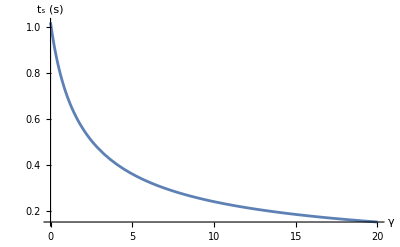

```mathematica
Plot[tsvalor/. {g->9.8,v0->10},{γ,0,20},PlotRange->All,AxesLabel->{"γ",HoldForm[Subscript[t,s] "(s)"]}]
```

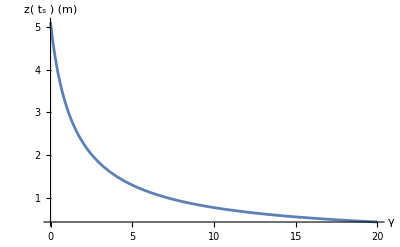

```mathematica
Plot[zMax/. {g->9.8,v0->10},{γ,0,20},PlotRange->All,AxesLabel->{"γ",HoldForm["z("Subscript[t,s]") (m)"]}]
```

Problema 3.5

A elaboração deste último gráfico foi totalmente análoga ao item anterior.

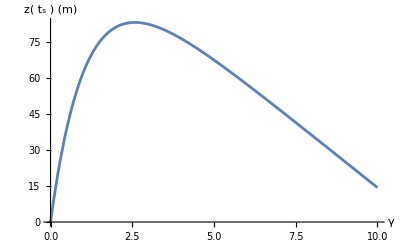

```mathematica
Plot[funcaoz/. {g->9.8,v0->100,γ->0.9},{t,0,10},PlotRange->All,AxesLabel->{"γ",HoldForm["z("Subscript[t,s]") (m)"] }]
```